```mathematica
SetDirectory[NotebookDirectory[]];
<<kinematic_utils.m
<<sylvester.m
```

```mathematica
subsc0={1+c1^2+c2^2+c3^2->c0}
subsc0sq={Expand[(1+c1^2+c2^2+c3^2)^2]->c0^2}
revsubsc0={c0-> 1+c1^2+c2^2+c3^2}
```

{1+c1^2+c2^2+c3^2→c0}

{1+2 c1^2+c1^4+2 c2^2+2 c1^2 c2^2+c2^4+2 c3^2+2 c1^2 c3^2+2 c2^2 c3^2+c3^4→c0^2}

{c0→1+c1^2+c2^2+c3^2}

```mathematica
(* Expression for the rotation matrix given c0,c1,c2,c3 *)
R=cayley2r[{c1,c2,c3}]/.subsc0;
R//MatrixForm
```

((1+c1^2-c2^2-c3^2)/c0 | (2 c1 c2-2 c3)/c0 | (2 (c2+c1 c3))/c0
(2 (c1 c2+c3))/c0 | (1-c1^2+c2^2-c3^2)/c0 | -(2 (c1-c2 c3))/c0
(2 (-c2+c1 c3))/c0 | (2 (c1+c2 c3))/c0 | (1-c1^2-c2^2+c3^2)/c0)

```mathematica
dummyexp[poly_,vars_,v_]:=Module[{mpoly,list,len,dumrule,dumpoly},
mpoly=monopoly[poly,vars];
len=Length[mpoly[[2]]];
list=Table[ToExpression[v<>ToString[i]],{i,1,len}];
dumrule=Inner[Rule,list,mpoly[[1]],List];
dumpoly=list.mpoly[[2]];
Return[{dumrule,dumpoly}];
];
```

### Architecture of the SRSPM

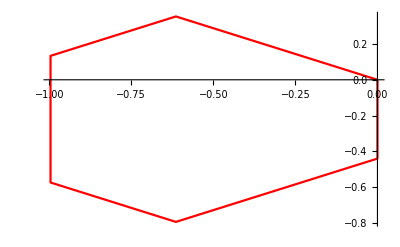

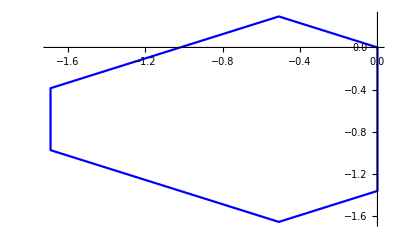

```mathematica
sub={b2x->-0.5093734006873172,b2y->0.2940868700048578,b3x->-1.6883547421176872,b3y->-0.3865983248395124,b4x->-1.6883547421176874,b4y->-0.9747720648492277,b5x->-0.5093734006873175,b5y->-1.6554572596935981,b6x->-2.220446049250313*10^-16,b6y->-1.3613703896887406,a2x->-0.6141031970306339,a2y->0.35455264611584647,a3x->-0.9961387846155708,a3y->0.13398429678366627,a4x->-0.996138784615571,a4y->-0.5751209954480264,a5x->-0.6141031970306341,a5y->-0.7956893447802065,a6x->-1.1102230246251565*10^-16,a6y->-0.44113669866436034};
(* Defining vertices of moving platform (with reference to local co-ordinate frame) *)
a1={0,0,0};
a2={a2x,a2y,0};
a3={a3x,a3y,0};
a4={a4x,a4y,0};
a5={a5x,a5y,0};
a6={a6x,a6y,0};
a={a1,a2,a3,a4,a5,a6,a1};
ListLinePlot[(a/.sub)[[;;, 1;;2]],PlotStyle->Red]

(* Defining vertices of fixed platform (with reference to global co-ordinate frame) *)
b1={0,0,0};
b2={b2x,b2y,0};
b3={b3x,b3y,0};
b4={b4x,b4y,0};
b5={b5x,b5y,0};
b6={b6x,b6y,0};
b={b1,b2,b3,b4,b5,b6,b1};
ListLinePlot[(b/.sub)[[;;, 1;;2]],PlotStyle->Blue]
```

```mathematica
(* Prismatic joint lengths for initial configuration *)
len={l1->1.2,l2->1.5,l3->1.6,l4->1.20833,l5->1.1,l6->1.3};
l={l1,l2,l3,l4,l5,l6};
```

```mathematica
p={px,py,pz};
subsleg1={p.p->l1^2};
```

#### Generate 5 equations, which are the leg constraints: (p_i+R.b_i-a_i).(p_i+R.b_i-a_i)-l_i^2

```mathematica
(* leg vectors *)
vec1=p+R.b1-a1;
vec2=p+R.b2-a2;
vec3=p+R.b3-a3;
vec4=p+R.b4-a4;
vec5=p+R.b5-a5;
vec6=p+R.b6-a6;
eqn1=Numerator[Together[Expand[vec1.vec1-l1^2]/.subsc0/.subsc0sq]];
eqn2=FactorList[Collect[Numerator[Together[Expand[vec2.vec2-l2^2]]],{c0,b2x,b2y}]/.subsc0/.subsc0sq/.subsleg1][[3,1]];
eqn2=Collect[eqn2,{c0,b2x,b2y}];
eqn3=FactorList[Collect[Numerator[Together[Expand[vec3.vec3-l3^2]]],{c0,b3x,b3y}]/.subsc0/.subsc0sq/.subsleg1][[3,1]];
eqn3=Collect[eqn3,{c0,b3x,b3y}];
eqn4=FactorList[Collect[Numerator[Together[Expand[vec4.vec4-l4^2]]],{c0,b4x,b4y}]/.subsc0/.subsc0sq/.subsleg1][[3,1]];
eqn4=Collect[eqn4,{c0,b4x,b4y}];
eqn5=FactorList[Collect[Numerator[Together[Expand[vec5.vec5-l5^2]]],{c0,b5x,b5y}]/.subsc0/.subsc0sq/.subsleg1][[3,1]];
eqn5=Collect[eqn5,{c0,b5x,b5y}];
eqn6=FactorList[Collect[Numerator[Together[Expand[vec6.vec6-l6^2]]],{c0,b6x,b6y}]/.subsc0/.subsc0sq/.subsleg1][[3,1]];
eqn6=Collect[eqn6,{c0,b6x,b6y}];
```

```mathematica
eqn1
```

-l1^2+px^2+py^2+pz^2

#### Solving 1 sphere and 5 planes intersection using homotopy continuation and NSolve

```mathematica
tempsol=NSolve[({eqn1,eqn2,eqn3,eqn4,eqn5,eqn6}/.revsubsc0/.len/.sub)=={0,0,0,0,0,0},{px,py,pz,c1,c2,c3},Method->"HomotopyContinuation"];
Dimensions[tempsol]
```

{40,6}

#### On verification if was observed that among the 40 solutions, for 8 of these c0=0.

```mathematica
Norm[vec1.vec1-l1^2]/.len/.sub/.tempsol
Norm[vec2.vec2-l2^2]/.revsubsc0/.len/.sub/.tempsol
Norm[vec3.vec3-l3^2]/.revsubsc0/.len/.sub/.tempsol
Norm[vec4.vec4-l4^2]/.revsubsc0/.len/.sub/.tempsol
Norm[vec5.vec5-l5^2]/.revsubsc0/.len/.sub/.tempsol
Norm[vec6.vec6-l6^2]/.revsubsc0/.len/.sub/.tempsol
```

{1.1692×10^50,1.1692×10^50,0.,0.,0.,0.,3.99629×10^46,3.99629×10^46,0.,0.,1.56105×10^44,1.56105×10^44,2.22184×10^-16,2.22184×10^-16,2.22059×10^-16,2.22059×10^-16,1.99883×10^-15,1.99883×10^-15,0.,0.,0.,0.,1.77636×10^-15,1.77636×10^-15,1.11022×10^-15,1.11022×10^-15,4.44124×10^-16,4.44124×10^-16,6.62062×10^-19,6.62062×10^-19,1.04083×10^-17,1.04083×10^-17,2.22045×10^-16,1.11022×10^-16,2.90695×10^-15,2.90695×10^-15,4.44089×10^-16,1.04083×10^-17,1.04083×10^-17,1.11022×10^-16}

{Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,1.1418×10^46,1.1418×10^46,Indeterminate,Indeterminate,1.11504×10^44,1.11504×10^44,1.50473×10^-17,1.50473×10^-17,8.88202×10^-16,8.88202×10^-16,4.44102×10^-15,4.44102×10^-15,4.47545×10^-16,4.47545×10^-16,4.47545×10^-16,4.47545×10^-16,7.10543×10^-15,7.10543×10^-15,1.11022×10^-15,1.11022×10^-15,4.4411×10^-16,4.4411×10^-16,8.88179×10^-16,8.88179×10^-16,6.245×10^-17,6.245×10^-17,0.,3.747×10^-16,2.61161×10^-15,2.61161×10^-15,4.44089×10^-16,6.245×10^-17,6.245×10^-17,5.82867×10^-16}

{Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,7.99259×10^46,7.99259×10^46,Indeterminate,Indeterminate,3.34511×10^44,3.34511×10^44,4.9982×10^-16,4.9982×10^-16,1.77638×10^-15,1.77638×10^-15,8.88727×10^-16,8.88727×10^-16,9.99201×10^-16,9.99201×10^-16,9.99201×10^-16,9.99201×10^-16,2.22045×10^-15,2.22045×10^-15,4.44089×10^-16,4.44089×10^-16,8.88214×10^-16,8.88214×10^-16,7.10544×10^-15,7.10544×10^-15,2.77556×10^-16,2.77556×10^-16,0.,1.11022×10^-16,1.42624×10^-15,1.42624×10^-15,0.,2.77556×10^-16,2.77556×10^-16,6.66134×10^-16}

{Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,3.99629×10^46,3.99629×10^46,Indeterminate,Indeterminate,1.56105×10^44,1.56105×10^44,1.77638×10^-15,1.77638×10^-15,1.77637×10^-15,1.77637×10^-15,3.70414×10^-17,3.70414×10^-17,6.20634×10^-16,6.20634×10^-16,6.20634×10^-16,6.20634×10^-16,1.33227×10^-15,1.33227×10^-15,4.44089×10^-16,4.44089×10^-16,9.54979×10^-18,9.54979×10^-18,3.55278×10^-15,3.55278×10^-15,4.47545×10^-16,4.47545×10^-16,6.66134×10^-16,6.66134×10^-16,1.34517×10^-15,1.34517×10^-15,6.66134×10^-16,4.47545×10^-16,4.47545×10^-16,6.66134×10^-16}

{Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,3.42539×10^46,3.42539×10^46,Indeterminate,Indeterminate,6.69022×10^43,6.69022×10^43,1.06583×10^-14,1.06583×10^-14,2.22047×10^-16,2.22047×10^-16,8.89296×10^-16,8.89296×10^-16,6.08727×10^-16,6.08727×10^-16,6.08727×10^-16,6.08727×10^-16,3.44169×10^-15,3.44169×10^-15,4.44089×10^-15,4.44089×10^-15,2.66455×10^-15,2.66455×10^-15,3.249×10^-18,3.249×10^-18,2.28878×10^-16,2.28878×10^-16,7.77156×10^-16,3.33067×10^-16,2.10805×10^-15,2.10805×10^-15,7.77156×10^-16,2.28878×10^-16,2.28878×10^-16,3.33067×10^-16}

{Indeterminate,Indeterminate,0.,0.,Indeterminate,Indeterminate,3.42539×10^46,3.42539×10^46,Indeterminate,Indeterminate,6.69022×10^43,6.69022×10^43,8.89542×10^-16,8.89542×10^-16,9.99203×10^-16,9.99203×10^-16,5.77334×10^-15,5.77334×10^-15,5.66105×10^-16,5.66105×10^-16,5.66105×10^-16,5.66105×10^-16,6.43929×10^-15,6.43929×10^-15,9.76996×10^-15,9.76996×10^-15,3.55272×10^-15,3.55272×10^-15,2.77586×10^-16,2.77586×10^-16,1.38778×10^-17,1.38778×10^-17,2.22045×10^-16,2.22045×10^-16,1.8596×10^-15,1.8596×10^-15,2.22045×10^-16,1.38778×10^-17,1.38778×10^-17,6.66134×10^-16}

```mathematica
eqn2a=Expand[eqn2]
eqn3a=Expand[eqn3]
eqn4a=Expand[eqn4]
```

-2 a2x b2x-2 a2y b2y+a2x^2 c0+a2y^2 c0+b2x^2 c0+b2y^2 c0-2 a2x b2x c1^2+2 a2y b2y c1^2-4 a2y b2x c1 c2-4 a2x b2y c1 c2+2 a2x b2x c2^2-2 a2y b2y c2^2-4 a2y b2x c3+4 a2x b2y c3+2 a2x b2x c3^2+2 a2y b2y c3^2+c0 l1^2-c0 l2^2+2 b2x px-2 a2x c0 px+2 b2x c1^2 px+4 b2y c1 c2 px-2 b2x c2^2 px-4 b2y c3 px-2 b2x c3^2 px+2 b2y py-2 a2y c0 py-2 b2y c1^2 py+4 b2x c1 c2 py+2 b2y c2^2 py+4 b2x c3 py-2 b2y c3^2 py+4 b2y c1 pz-4 b2x c2 pz+4 b2x c1 c3 pz+4 b2y c2 c3 pz

-2 a3x b3x-2 a3y b3y+a3x^2 c0+a3y^2 c0+b3x^2 c0+b3y^2 c0-2 a3x b3x c1^2+2 a3y b3y c1^2-4 a3y b3x c1 c2-4 a3x b3y c1 c2+2 a3x b3x c2^2-2 a3y b3y c2^2-4 a3y b3x c3+4 a3x b3y c3+2 a3x b3x c3^2+2 a3y b3y c3^2+c0 l1^2-c0 l3^2+2 b3x px-2 a3x c0 px+2 b3x c1^2 px+4 b3y c1 c2 px-2 b3x c2^2 px-4 b3y c3 px-2 b3x c3^2 px+2 b3y py-2 a3y c0 py-2 b3y c1^2 py+4 b3x c1 c2 py+2 b3y c2^2 py+4 b3x c3 py-2 b3y c3^2 py+4 b3y c1 pz-4 b3x c2 pz+4 b3x c1 c3 pz+4 b3y c2 c3 pz

-2 a4x b4x-2 a4y b4y+a4x^2 c0+a4y^2 c0+b4x^2 c0+b4y^2 c0-2 a4x b4x c1^2+2 a4y b4y c1^2-4 a4y b4x c1 c2-4 a4x b4y c1 c2+2 a4x b4x c2^2-2 a4y b4y c2^2-4 a4y b4x c3+4 a4x b4y c3+2 a4x b4x c3^2+2 a4y b4y c3^2+c0 l1^2-c0 l4^2+2 b4x px-2 a4x c0 px+2 b4x c1^2 px+4 b4y c1 c2 px-2 b4x c2^2 px-4 b4y c3 px-2 b4x c3^2 px+2 b4y py-2 a4y c0 py-2 b4y c1^2 py+4 b4x c1 c2 py+2 b4y c2^2 py+4 b4x c3 py-2 b4y c3^2 py+4 b4y c1 pz-4 b4x c2 pz+4 b4x c1 c3 pz+4 b4y c2 c3 pz

```mathematica
solxy=Solve[({eqn2a,eqn3a}/.revsubsc0)=={0,0},{px,py}][[1]];
```

#### Exponents of c1,c2,c3, in the analytical solutions of px,py,pz obtained by solving the intersection of 3 circles.

```mathematica
Exponent[Numerator[Together[(px/.solxyz)]],{c0,c1,c2,c3}]
Exponent[Denominator[Together[(px/.solxyz)]],{c0,c1,c2,c3}]
```

{0,3,3,3}

{0,3,3,3}

```mathematica
Exponent[Numerator[Together[(py/.solxyz)]],{c0,c1,c2,c3}]
Exponent[Denominator[Together[(py/.solxyz)]],{c0,c1,c2,c3}]
```

{0,3,3,3}

{0,3,3,3}

```mathematica
Exponent[Numerator[Together[(pz/.solxyz)]],{c0,c1,c2,c3}]
Exponent[Denominator[Together[(pz/.solxyz)]],{c0,c1,c2,c3}]
```

{0,4,4,4}

{0,3,3,3}

#### Auxiliary translation vector is introduced:

```mathematica
q={qx,qy,qz}
qvec=Transpose[R].p
subsq={Expand[Numerator[Together[qvec[[1]]]]]->c0*qx,Expand[Numerator[Together[qvec[[2]]]]]->c0*qy,Expand[Numerator[Together[qvec[[3]]]]]->c0*qz}
```

{qx,qy,qz}

{((1+c1^2-c2^2-c3^2) px)/c0+(2 (c1 c2+c3) py)/c0+(2 (-c2+c1 c3) pz)/c0,((2 c1 c2-2 c3) px)/c0+((1-c1^2+c2^2-c3^2) py)/c0+(2 (c1+c2 c3) pz)/c0,(2 (c2+c1 c3) px)/c0-(2 (c1-c2 c3) py)/c0+((1-c1^2-c2^2+c3^2) pz)/c0}

{px+c1^2 px-c2^2 px-c3^2 px+2 c1 c2 py+2 c3 py-2 c2 pz+2 c1 c3 pz→c0 qx,2 c1 c2 px-2 c3 px+py-c1^2 py+c2^2 py-c3^2 py+2 c1 pz+2 c2 c3 pz→c0 qy,2 c2 px+2 c1 c3 px-2 c1 py+2 c2 c3 py+pz-c1^2 pz-c2^2 pz+c3^2 pz→c0 qz}

#### Substituting the auxiliary translation vector

#### 3 linear equations in px,py,pz,qx,qy,qz using q=R^T p and R=(I_3-c)^-1(I_3+c)

```mathematica
(* c is the skew symmetric matrix corresponding to {c1,c2,c3} *)
c={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}};
```

```mathematica
eqnlist1=-(IdentityMatrix[3]-c).p+(IdentityMatrix[3]+c).q;
eqn12=eqnlist1[[1]]
eqn13=eqnlist1[[2]]
eqn14=eqnlist1[[3]]
```

-px-c3 py+c2 pz+qx-c3 qy+c2 qz

c3 px-py-c1 pz+c3 qx+qy-c1 qz

-c2 px+c1 py-pz-c2 qx+c1 qy+qz